## Triangular Navigation

Equal Bearing navigation

#### moving at a set velocity, try to turn so that the bearing from the stationary robots to the is equal

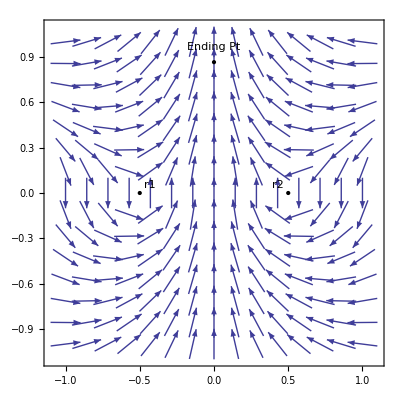

```mathematica
r1 = {-1/2,0};
r2 = {1/2,0};
rd = {0,(√3)/2};
MBAngR2[x_,y_]:=(A = r1-r2;B={x,y}-r2;ArcCos[(A.B)/(Norm[A,2]Norm[B,2])])(*ArcTan[x-r2⟦2⟧, y-r2⟦1⟧];*)
MBAngR1[x_,y_]:=(A = r2-r1;B={x,y}-r1;ArcCos[(A.B)/(Norm[A,2]Norm[B,2])])(*ArcTan[x-r1⟦2⟧, y-r1⟦1⟧];*)
MeanBAng[x_,y_]:=π/2+(-MBAngR1[x,y]+MBAngR2[x,y]);
VectorPlot[{Cos[MeanBAng[x,y]],Sin[MeanBAng[x,y]]},{x,-1,1},{y,-1,1},Epilog->{PointSize[Large],Point[{r1,r2,rd}],Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",rd+{0,.1}]}]
```

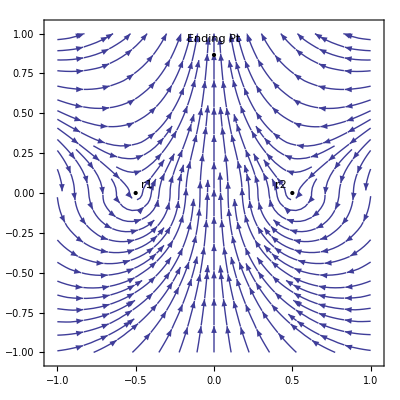

```mathematica
StreamPlot[{Cos[MeanBAng[x,y]],Sin[MeanBAng[x,y]]},{x,-1,1},{y,-1,1},TicksStyle->Directive[24],Epilog->{PointSize[Large],Point[{r1,r2,rd}],Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",rd+{0,.1}]}]
```

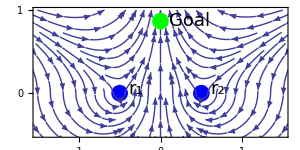

```mathematica
fsz = 18;
StreamPlot[{Cos[MeanBAng[x,y]],Sin[MeanBAng[x,y]]},{x,-2,2},{y,-1,1},
Ticks->{{-1,0,1},{0,1}},
TicksStyle->Directive[24],
PlotRange->{{-1.5,1.5},{-.5,1}},AspectRatio->1.5/3,ImageSize->300,
Prolog->{PointSize[0.04],Green, Point[{rd}],
Blue, Point[{r1,r2}]},
FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},
FrameTicksStyle->Directive[fsz],
(*StreamScale->Medium,*)
Epilog->{
Text[Style[" r_1",fsz],r1+{0.2,0.05},Background->White],
Text[Style[" r_2 ",fsz],r2+{0.2,0.05},Background->White],
Text[Style["Goal",fsz],rd+{0.35,0},Background->White]}
]
```

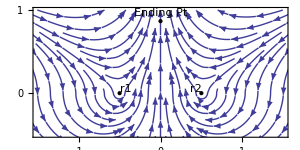

Mid - Angle Navigation

#### Try to move so that bearing to stationary robots is equal.

```mathematica
r1 = {-1/2,0};
r2 = {1/2,0};
MAngR2[x_,y_]:=ArcTan[r2⟦1⟧-x,r2⟦2⟧-y];
MAngR1[x_,y_]:=ArcTan[r1⟦1⟧-x, r1⟦2⟧-y];

MeanAng[x_,y_]:=Piecewise[{{(MAngR1[x,y]+MAngR2[x,y])/2,y<0},{- (MAngR1[x,y]+MAngR2[x,y])/2,y≥ 0}}];

VectorPlot[{Cos[MeanAng[x,y]],Sin[MeanAng[x,y]]},{x,-1,1},{y,-1,1},Epilog->{PointSize[Large],Point[{r1,r2,rd}],Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",robotEndingPt+{0,.1}]}]
```

-Graphics-

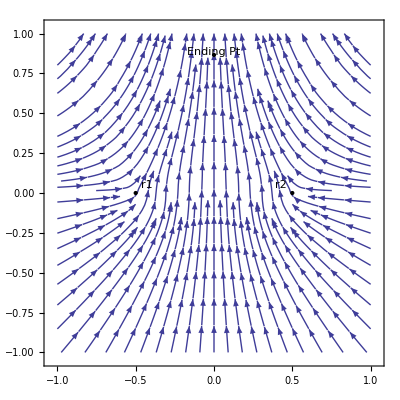

```mathematica
StreamPlot[{Cos[MeanAng[x,y]],Sin[MeanAng[x,y]]},{x,-1,1},{y,-1,1},Epilog->{PointSize[Large],Point[{r1,r2,rd}],Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",robotEndingPt+{0,.1}]}]
```

## Discrete Sector Navigation

```mathematica
r1 = {-1/2,0};
r2 = {1/2,0};
rd = {0,(√3)/2};
```

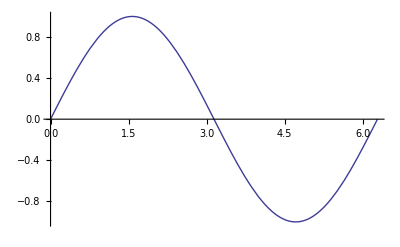

```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
TriangulateY[ell_, α_,β_] := If[Sin[α+β] ==0,0,(ell Sin[α]Sin[β])/Sin[α+β]](*vertical height of triangle, alpha is internal angle from left corner between right and object*)
TriangulateX[ell_, α_,β_] :=If[Sin[α+β] ==0,ell/2, ell Cos[α] Csc[α+β] Sin[β]](*horizontal distance from left corner*)
```

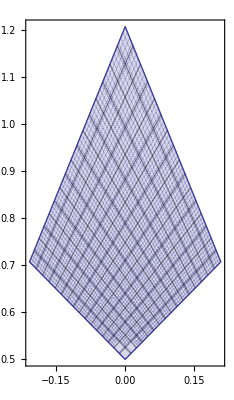

```mathematica
possibleEndingRegion=ParametricPlot[{-1/2+TriangulateX[1, θ1,θ2] ,TriangulateY[1, θ1,θ2] },{θ1,(5π)/16+-π/16,(5π)/16+π/16},{θ2,(5π)/16+-π/16,(5π)/16+π/16}]
```

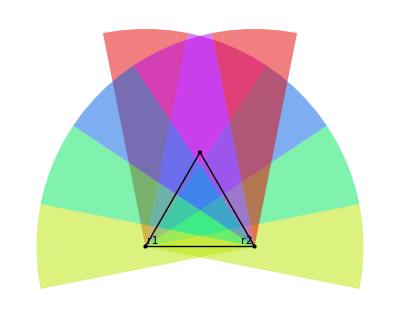

```mathematica
Graphics[{Table[{Hue[k/5,1,.9,.5],Disk[r1,2,{θ1+k π/8,θ1+(k-1)π/8}]},{k,1,5}],
Table[{Hue[k/5,1,.9,.5],Disk[r2,2,{θ2+π-k π/8,θ2+π-(k-1)π/8}]},{k,1,5}],
Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
}]/.{θ1 ->-π/16, θ2->π/16}
```

```mathematica
Manipulate[robotEndingPt = {-1/2+TriangulateX[1, θ1+(6π)/16,(6π)/16-θ2] ,TriangulateY[1, θ1+(6π)/16,(6π)/16-θ2]};
Show[Graphics[{Table[{Hue[k/5,1,.9,.5],Disk[r1,2,{θ1+k π/8,θ1+(k-1)π/8}]},{k,1,5}],
Table[{Hue[k/5,1,.9,.5],Disk[r2,2,{θ2+π-k π/8,θ2+π-(k-1)π/8}]},{k,1,5}],
Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",robotEndingPt+{0,.05}],
Red,Point[robotEndingPt]
},PlotRange->{{-1.7,1.7},{-.4,2}},ImageSize->Large],possibleEndingRegion],{{θ1,-π/16},-π/8,0},{{θ2,π/16},0,π/8}]
```

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[r1, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[r1, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[r1, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[r1, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[r1, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]]], List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[r2, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[r2, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[r2, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[r2, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[r2, 2, List[Times[Skeleton[2]], Times[Skeleton[2]]]]]], GrayLevel[0], LineBox[List[r1, rd, r2, r1]], PointSize[Large], PointBox[List[r1, r2, rd]], InsetBox[FormBox[.

Couldn't we have robot 1 servo to center its IR on robot 2, and robot 2 servo to center it's IR on 1?
We want the intersection of 5 π/16 from left and 11 π/16 from right

```mathematica
N[2/8]
N[5/16]
N[3/8]
```

0.25

0.3125

0.375

```mathematica
N[1/3]
```

## Determine probability density f_(x,y)(x,y)

```mathematica
need to do a change in variables...  I can do this in two equivalent ways..... it's been a long time since this math class..
```

```mathematica
pdfΘ[θ1_,θ2_]:= 64/π^2(*1/(π/8 π/8)*)
```

```mathematica
16 Abs[y/(16 x^4+8 x^2 (-1+4 y^2)+(1+4 y^2)^2)]
```

```mathematica
Triangulateα[x_,y_] :=ArcTan[y/x];
Triangulateβ[x_,y_] := ArcTan[y/(1-x)];
Triangulateα1[x_,y_] :=ArcTan[y/(1/2+x)];
Triangulateβ1[x_,y_] := ArcTan[y/(1/2-x)];
```

```mathematica
JacobXY = D[{Triangulateα[x,y],Triangulateβ[x,y]},{{x,y}}];
FullSimplify[Abs[Det[JacobXY]]]
```

Abs[y/(((-1+x)^2+y^2) (x^2+y^2))]

```mathematica
Clear[θ1,θ2]
Jacob = D[{TriangulateX[1, θ1,θ2],TriangulateY[1, θ1,θ2]},{{θ1,θ2}}];
FullSimplify[Abs[Det[Jacob]]]
```

Abs[Csc[θ1+θ2]^3 Sin[θ1] Sin[θ2]]

```mathematica
r1d = {-1/2,0,0};
r2d = {1/2,0,0};
rdd = {0,(√3)/2,0};
```

### First way to do change of variables to find the pdf

```mathematica
Show[{ParametricPlot3D[{-1/2+TriangulateX[1, θ1,θ2] ,TriangulateY[1, θ1,θ2] ,64/π^2 1/Abs[Csc[θ1+θ2]^3 Sin[θ1] Sin[θ2]]},{θ1,(5π)/16+-π/16,(5π)/16+π/16},{θ2,(5π)/16+-π/16,(5π)/16+π/16},PlotRange->All,AxesOrigin->{0,0,0},BoxRatios->{1,1.2,1}]
,Graphics3D[{PointSize[Large],Point[{r1d,r2d,rdd}],
Text["r1",r1d+{0.07,0.05,0}],Text["r2",r2d+{-0.07,0.05,0}],
Line[{rdd,r1d,r2d,rdd}],
Line[{rdd,rdd+{0,0,10}}],Red,Point[{rdd+{0,0,10}}]
}]
}]
```

-Graphics3D-

### Second way to do change of variables to find the pdf (equivalent)

```mathematica
Show[{ParametricPlot3D[{-1/2+TriangulateX[1, θ1,θ2] ,TriangulateY[1, θ1,θ2] ,64/π^2 Abs[y/(((-1+x)^2+y^2) (x^2+y^2))]/.{x->TriangulateX[1, θ1,θ2] ,y->TriangulateY[1, θ1,θ2]}},{θ1,(5π)/16+-π/16,(5π)/16+π/16},{θ2,(5π)/16+-π/16,(5π)/16+π/16},PlotRange->All,BoundaryStyle->Directive[Thick,Blue],AxesOrigin->{0,0,0},BoxRatios->{1,1.2,1}]
,Graphics3D[{PointSize[Large],Point[{r1d,r2d,rdd}],
Text["r1",r1d+{0.07,0.05,0}],Text["r2",r2d+{-0.07,0.05,0}],
Line[{rdd,r1d,r2d,rdd}],
Line[{rdd,rdd+{0,0,10}}],Red,Point[{rdd+{0,0,10}}]
}]
}]
```

-Graphics3D-

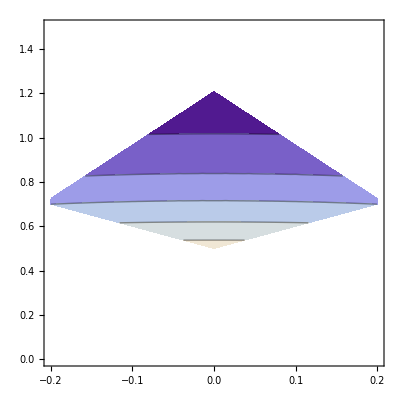

```mathematica
ContourPlot[64/π^2 16 Abs[y/(16 x^4+8 x^2 (-1+4 y^2)+(1+4 y^2)^2)],{x,-.2,.2},{y,0,1.5},RegionFunction->Function[{x,y,z},Triangulateα1[x,y]≤ (5π)/16+π/16&& Triangulateα1[x,y]≥ (5π)/16-π/16&& Triangulateβ1[x,y]≤ (5π)/16+π/16&& Triangulateβ1[x,y]≥ (5π)/16-π/16]]
```

## monteCarlo Simulation (for cross checking)

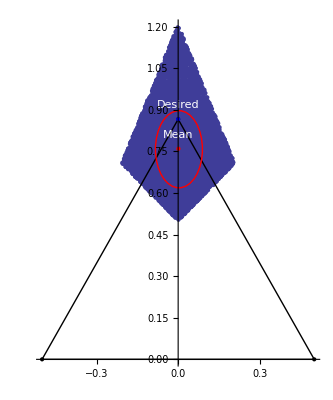

{0.0863082,0.139093}

```mathematica
pairs=Table[{-1/2+TriangulateX[1, θ1,θ2] ,TriangulateY[1, θ1,θ2] }/.{ θ1->RandomReal[{(5π)/16+-π/16,(5π)/16+π/16}],θ2->RandomReal[{(5π)/16+-π/16,(5π)/16+π/16}]},{10000}];
lp=ListPlot[pairs,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-.5,.5},{0,1.2}},Epilog->{PointSize[Large],Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}],Blue, Point[rd],White,Text["Desired",rd+{0,.05}],Red,Point[Mean[pairs]],Circle[Mean[pairs],StandardDeviation[pairs]],White,Text["Mean",Mean[pairs]+{0,.05}]}]
StandardDeviation[pairs]
```

```mathematica
Histogram3D[pairs,Automatic,"ProbabilityDensity",PlotRange->All,AxesOrigin->{0,0,0},BoxRatios->{1,2,1}]
```

-Graphics3D-

```mathematica
SmoothDensityHistogram[pairs]
```

## Discrete Motion Planning

```mathematica
Label the cells
draw just the cells
```

```mathematica
TriangulateY[ell_, α_,β_] 
TriangulateX[ell_, α_,β_]
```

```mathematica
StringForm["``,``",3,4] If[Sin[α+β]≠ 0,
/.{θ1 ->-π/16, θ2->π/16}
```

```mathematica
{TriangulateX[1,0,0] ,TriangulateY[1, 0,0] }
```

{0,0}

```mathematica
Manipulate[Graphics[{Table[{
A1 = θ1+(k+1) π/8;
B1 = θ2+π-(k+1) π/8;
Text[StringForm["``,0",k],r1+.18{Cos[A1 -π/16],Sin[A1-π/16]}],
Text[StringForm["0,``",k],r2+.18{Cos[B1+π/16],Sin[B1+π/16]}],
{Hue[k/16,1,.9,.4],Disk[r1,2,{A1 ,A1 -π/8}]},
{Hue[k/16,1,.9,.4],Disk[r2,2,{B1,B1+π/8}]}
},{k,-7,8}],
(*label the 4-sided cells*)
Table[Table[A1 = θ1+(k+1)  π/8;
α = A1 -π/16;β = θ2+π-(n+1)π/8+π/16;
x = TriangulateX[1, α,β];
y=TriangulateY[1, α,β];
Text[StringForm["``,``",k,-n],If[(k==0&&-n==0)||(k>0&&-n>0&& y>0) || (k<0&&-n<0&& y<0) ,r1+{x ,y },{-3,0}]]
 ,{n,-7,8}],{k,-7,8}],

Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
},ImageSize->1200,PlotRange->{{-2.5,2.5},{-2,2}}]/.{θ1 ->-π/16, θ2->π/16},{{θ1,-π/16},-π/8,0},{{θ2,π/16},0,π/8}]
```

```mathematica
Manipulate[Graphics[{Table[{
A1 = θ1+(k+1) π/8;
B1 = θ2+π-(k+1) π/8;
Text[StringForm["``,0" ,k],If[k==0,{-5,0},r1+.18{Cos[A1 -π/16],Sin[A1-π/16]}]],
Text[StringForm["0,``",k],If[k==0,{-5,0},r2+.18{Cos[B1+π/16],Sin[B1+π/16]}]],
Line[{r1,r1+4{Cos[A1],Sin[A1]}}],
Line[{r2,r2+4{Cos[B1],Sin[B1]}}]
},{k,-7,8}],
(*label the 4-sided cells*)
Table[Table[A1 = θ1+(k+1)  π/8;
α = A1 -π/16;β = θ2+π-(n+1)π/8+π/16;
x = TriangulateX[1, α,β];
y=TriangulateY[1, α,β];
Text[StringForm["``,``",k,-n],If[(k==0&&-n==0)||(k>0&&-n>0&& y>0) || (k<0&&-n<0&& y<0) ,r1+{x ,y },{-3,0}]]
 ,{n,-7,8}],{k,-7,8}],

Blue,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
},ImageSize->800,PlotRange->{{-1.5,1.5},{-1,1.3}}]/.{θ1 ->-π/16, θ2->π/16},{{θ1,-π/16},-π/8,0},{{θ2,π/16},0,π/8}]
```

Construction:

    cell (0, 0) is a quadrilateral rooted at r1 and r2
    Cells (*,0) and (0,*)) are triangles rooted at  r1 and r2, and * = {-7,8,7} are not guaranteed to exist. (in those cases, simply orbit perpendicular to the stationary robot)

Discrete Motion plan: The goal is the crossing between (2,2) and (3,3)

    cells of the form (k,k), move up k<3 or down k >= 3 to goal,
    cells (2,3) move right and (3,2) move left 
    negative triangles, orbit toward (0,0),
    all other negative cells move to (-1,-1)
    Positive cells, move toward goal..

## Using 9 IR sensors instead of 8 -- you’d need the stationary robots to align along a switching point

```mathematica
TriangulateY[ell_, α_,β_] := If[Sin[α+β] ==0,0,(ell Sin[α]Sin[β])/Sin[α+β]](*vertical height of triangle, alpha is internal angle from left corner between right and object*)
TriangulateX[ell_, α_,β_] :=If[Sin[α+β] ==0,ell/2, ell Cos[α] Csc[α+β] Sin[β]](*horizontal distance from left corner*)
```

```mathematica
sectorSize = π/9;
```

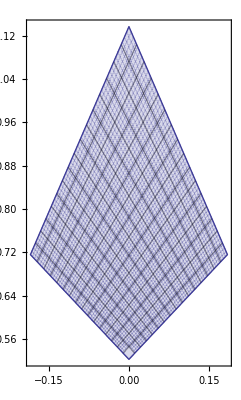

```mathematica
possibleEndingRegion2[sectorSize_]:=ParametricPlot[{-1/2+TriangulateX[1, θ1,θ2] ,TriangulateY[1, θ1,θ2] },{θ1,(5π)/16-sectorSize/2,(5π)/16+sectorSize/2},{θ2,(5π)/16-sectorSize/2,(5π)/16+sectorSize/2}];
possibleEndingRegion2[π/9]
```

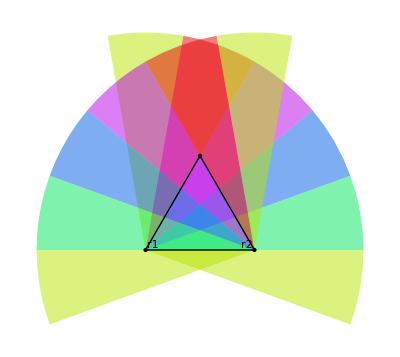

```mathematica
sectorSize = π/9;
Graphics[{Table[{Hue[k/5,1,.9,.5],Disk[r1,2,{θ1+k sectorSize,θ1+(k-1)sectorSize}]},{k,1,6}],
Table[{Hue[k/5,1,.9,.5],Disk[r2,2,{θ2+π-k sectorSize,θ2+π-(k-1)sectorSize}]},{k,1,6}],
Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
}]/.{θ1 ->-sectorSize, θ2->sectorSize}
```

```mathematica
sectorSize = π/9;
Manipulate[robotEndingPt = {-1/2+TriangulateX[1, θ1+(6π)/16,(6π)/16-θ2] ,TriangulateY[1, θ1+(6π)/16,(6π)/16-θ2]};
Show[Graphics[{Table[{Hue[k/5,1,.9,.5],Disk[r1,2,{θ1+k sectorSize,θ1+(k-1)sectorSize}]},{k,1,6}],
Table[{Hue[k/5,1,.9,.5],Disk[r2,2,{θ2+π-k sectorSize,θ2+π-(k-1)sectorSize}]},{k,1,6}],
Black,Line[{r1,rd,r2,r1}],PointSize[Large],Point[{r1,r2,rd}], Text["r1",r1+{0.07,0.05}],Text["r2",r2+{-0.07,0.05}],
Text["Ending Pt",robotEndingPt+{0,.05}],
Red,Point[robotEndingPt]
},PlotRange->{{-1.7,1.7},{-.4,2}},ImageSize->Large],possibleEndingRegion2[sectorSize]],{{θ1,-sectorSize/2},-sectorSize,0},{{θ2,sectorSize/2},0,sectorSize}]
```

ParametricPlot::plln: Limiting value 5\ π/16 - sectorSize/2 in {θ1, 5\ π/16 - sectorSize/2, 5\ π/16 + sectorSize/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], 0.`]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[6, 5], 1.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]]], List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], 3.490658503988659`]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[6, 5], 1.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]]], GrayLevel[0], LineBox[NCache[List[List[Rational[-1, 2], 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]], List[Rational[1, 2], 0], List[Rational[-1, 2], 0]], List[List[-0.5`, 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]], List[0.5`, 0], List[-0.5`, 0]]]], PointSize[Large], PointBox[NCache[List[List[Rational[-1, 2], 0], List[Rational[1, 2], 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]]], List[List[-0.5`, 0], List[0.5`, 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]]]]], InsetBox[FormBox[.

ParametricPlot::plln: Limiting value 5\ π/16 - sectorSize/2 in {θ1, 5\ π/16 - sectorSize/2, 5\ π/16 + sectorSize/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], 0.`]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[6, 5], 1.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[-1, 2], 0], List[-0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]]], List[List[Hue[NCache[Rational[1, 5], 0.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], 3.490658503988659`]]], List[Hue[NCache[Rational[2, 5], 0.4`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[3, 5], 0.6`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[4, 5], 0.8`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[1, 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]], List[Hue[NCache[Rational[6, 5], 1.2`], 1, 0.9`, 0.5`], DiskBox[NCache[List[Rational[1, 2], 0], List[0.5`, 0]], 2, List[Plus[Skeleton[2]], Plus[Skeleton[2]]]]]], GrayLevel[0], LineBox[NCache[List[List[Rational[-1, 2], 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]], List[Rational[1, 2], 0], List[Rational[-1, 2], 0]], List[List[-0.5`, 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]], List[0.5`, 0], List[-0.5`, 0]]]], PointSize[Large], PointBox[NCache[List[List[Rational[-1, 2], 0], List[Rational[1, 2], 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]]], List[List[-0.5`, 0], List[0.5`, 0], List[0, Times[Rational[1, 2], Power[Skeleton[2]]]]]]], InsetBox[FormBox[.